# A Card Trick

Text from:
http://jeremyclark.wordpress.com/2007/08/10/a-card-trick/

An article by John Allen Paulos tipped me off to an interesting card trick. The trick is mathematical, and based on probability theory not sleight of hand. You get rid of the face cards in a deck (leaving the aces, which will be treated as 1’s), and give it a good shuffle. You then tell someone you are trying to impress to pick a secret number between 1 and 10. Let’s say she picks 7—after all, we all know that prime numbers are more random ;) . You then ask her to count (from 1… if she is geeky enough to count from 0, she’s probably not going to find the trick very impressive) the cards as you slowly turn them over. When the cards reach her number, the 7th card, she looks at the number on the card and this her new secret number. She then starts counting cards again from 1 to her new number, and repeats the process. Towards the end of the deck, you pause after overturning a card, tap it, and declare it to be the secret card she was counting towards.

The trick is to do the same thing you’ve ask her to do with the first card and go through the process in your head as you are performing the trick. The probability is in favor of your chain of numbers colliding at some point with hers, after which every number in the sequence will be the same (the chains have been “coupled”). As you near the end of the deck, you guess your own secret card with the confidence that it will be the same as hers.

To see it in action, here is a graph showing how such a game might progress. The numbers on the graph are not the series of secret numbers themselves, but rather the position of the secret cards in the deck.

If you run it a few times, you'll see that sometimes, it doesn’t work out perfectly.

So what is the probability that the trick will actually work? Working out the solution is more difficult than it sounds, but it has been found empirically to be about 83.7% for this variation (other variations leave the face cards in, and have them count as 5’s, raising the probability of succeeding a couple points).

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Shuffled Deck: {6,1,8,5,7,2,1,5,10,6,2,6,9,4,8,7,4,7,9,10,6,3,5,3,3,1,10,1,4,9,9,8,10,8,7,3,4,2,5,2}

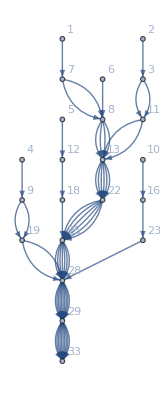

Entropy of the outcome: 0.

```mathematica
(* Parameters *)
n=10;
m=4;

(* Packages *)
Needs["Combinatorica`"];

(* Code *)

deck=Flatten[Table[Range[1,n],{m}]]//RandomPermutation;

Print["\n\nShuffled Deck: ",%];

f[x_]:=NestWhileList[deck[[#]]+#&,x,deck[[#]]+#≤Length[deck]&]

g[x_]:=Rule@@#&/@Transpose[{Most[x],Rest[x]}]

h[x_]:=g/@f/@Range[x]//Flatten;

h[n];

LayeredGraphPlot[%,DirectedEdges->True,VertexLabeling->True,MultiedgeStyle->0.3,PackingMethod->"LayeredTop"]


ent[x_]:=-x*Log[2,x]
Last/@f/@Range[n];
DeleteCases[BinCounts[%,1],0];
N[Total[ent/@(%/10)]];
Print["Entropy of the outcome: ", %];
```